```mathematica
SetOptions[Plot,BaseStyle->FontSize->20];
SetOptions[ContourPlot,BaseStyle->{FontSize->20, FontColor ->  Black}];
SetOptions[ListContourPlot,BaseStyle->{FontSize->20, FontColor ->  Black}];
SetOptions[ListLinePlot,BaseStyle->{FontSize->20, FontColor ->  Black}];
```

```mathematica
hbar=1.05457148×10(10)^-34; Delta = 9.2 10^12;Gam = 32.8 10^6/(2 Pi);λ = 852.1 10^-9; Inti = 2000000;Ints = 3;mCs = (133 1.660 10^-27);Er = hbar^2 k^2/(2*mCs);
alal = 2;k= 2 Pi/λ;
el = 1.602 10^-19;
me = 9.1 10^-31;
```

```mathematica
Clear[a,b,x,y,z,r, hbar, Gam, Inti, Ints, Delta,k]
```

```mathematica
UDsim[x_,y_,z_,a_,b_]:=-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])
```

```mathematica
ϵ1 = {r Exp[-ⅈ*k*z], Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z]+ ⅈ r Exp[-ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y] }
ϵ1s = {r Exp[+ⅈ*k*z], Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z]- ⅈ r Exp[+ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}
```

{ⅇ^(-ⅈ k z) r,ⅇ^(ⅈ k z)+ⅈ ⅇ^(-ⅈ k z) r+ⅇ^(ⅈ k x) Sin[a]+ⅇ^(-ⅈ k x) Sin[b],ⅇ^(ⅈ k y)+ⅇ^(ⅈ k x) Cos[a]+ⅇ^(-ⅈ k x) Cos[b]}

{ⅇ^(ⅈ k z) r,ⅇ^(-ⅈ k z)-ⅈ ⅇ^(ⅈ k z) r+ⅇ^(-ⅈ k x) Sin[a]+ⅇ^(ⅈ k x) Sin[b],ⅇ^(-ⅈ k y)+ⅇ^(-ⅈ k x) Cos[a]+ⅇ^(ⅈ k x) Cos[b]}

```mathematica
ecrossold = +1/3*hbar Gam^2 Inti / (Delta*8 Ints)ⅈ*Cross[{0, Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]},{0, Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}]//FullSimplify
```

{1/(12 Delta Ints)Gam^2 hbar Inti (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}

```mathematica
ecrosssold = {1/(12 Delta Ints)Gam^2 hbar Inti (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}
```

{1.73542×10^-28 (-Sin[7.37377×10^6 (x-y)]/(√2)+Sin[7.37377×10^6 y]+Sin[7.37377×10^6 (x+y)]/(√2)),0,0}

```mathematica
+1/3*hbar Gam^2 Inti / (Delta*8 Ints)
```

```mathematica
ecross =  ⅈ*Cross[ϵ1,ϵ1s]//FullSimplify
```

{-2 (r Cos[k (y+z)]+Sin[a-b] Sin[2 k x]+Sin[a] Sin[k (x-y)]-Sin[b] Sin[k (x+y)]+Cos[a] (r Cos[k (x+z)]-Sin[k (x-z)])-Sin[k (y-z)]+Cos[b] (r Cos[k (x-z)]+Sin[k (x+z)])),2 r (Cos[b] Sin[k (x-z)]-Cos[a] Sin[k (x+z)]-Sin[k (y+z)]),2 r (r+Cos[k z] (Sin[a]-Sin[b]) Sin[k x]+Cos[k x] (Sin[a]+Sin[b]) Sin[k z]+Sin[2 k z])}

```mathematica
ecrosss[x_,y_,z_,a_,b_] := +1/3*hbar Gam^2 Inti / (Delta*8 Ints){-2 (r Cos[k (y+z)]+Sin[a-b] Sin[2 k x]+Sin[a] Sin[k (x-y)]-Sin[b] Sin[k (x+y)]+Cos[a] (r Cos[k (x+z)]-Sin[k (x-z)])-Sin[k (y-z)]+Cos[b] (r Cos[k (x-z)]+Sin[k (x+z)])),2 r (Cos[b] Sin[k (x-z)]-Cos[a] Sin[k (x+z)]-Sin[k (y+z)]),2 r (r+Cos[k z] (Sin[a]-Sin[b]) Sin[k x]+Cos[k x] (Sin[a]+Sin[b]) Sin[k z]+Sin[2 k z])}
```

```mathematica
r=0;Plot3D[ecrosss[x,y,0,Pi/4,Pi/2][[1]] 10^50,{x,-λ/2,λ/2},{y,-λ/2,λ/2}]
```

-Graphics3D-

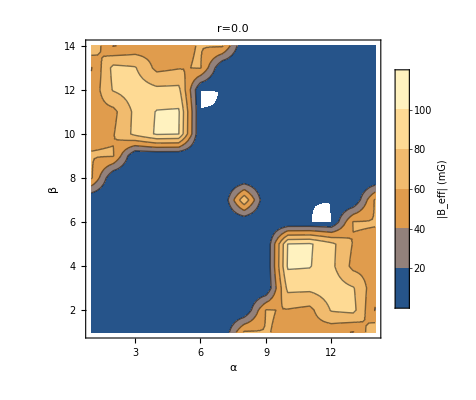

```mathematica
r=0.0;
ListContourPlot[ Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1, PlotLabel -> "r=0.0"]
```

```mathematica
Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/5},{y,-1λ/2,1λ/2,λ/5},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}]
```

{{9.81229×10^-15,7.27397×10^-15,4.503×10^-15,1.66042×10^-15,1.08858×10^-15,3.58423×10^-15,5.68149×10^-15,62.5649,60.7536,57.2361,52.2169,45.9878,38.9107,76.2019},{1.21605×10^-14,9.62221×10^-15,6.76026×10^-15,3.741×10^-15,7.39899×10^-16,2.06862×10^-15,4.52135×10^-15,6.47574×10^-15,61.2031,58.5387,54.2703,48.6462,85.7781,38.9107},{1.43723×10^-14,1.1925×10^-14,9.063×10^-15,5.95276×10^-15,2.77499×10^-15,2.85631×10^-16,3.05123×10^-15,5.36108×10^-15,7.08095×10^-15,58.1023,91.9928,90.598,48.6462,45.9878},{1.6319×10^-14,1.40484×10^-14,1.12774×10^-14,8.16717×10^-15,4.89842×10^-15,1.66112×10^-15,1.35658×10^-15,3.9793×10^-15,6.05463×10^-15,100.943,89.42,91.9928,54.2703,52.2169},{1.78877×10^-14,1.58691×10^-14,1.32748×10^-14,1.02555×10^-14,6.98678×10^-15,3.6585×10^-15,4.64128×10^-16,2.4107×10^-15,4.7989×10^-15,4.44888×10^-15,100.943,58.1023,58.5387,57.2361},{1.89869×10^-14,1.72813×10^-14,1.49391×10^-14,1.20965×10^-14,8.9187×10^-15,5.59042×10^-15,2.30507×10^-15,7.46429×10^-16,5.41058×10^-16,3.71601×10^-15,6.67501×10^-15,9.24607×10^-15,61.2031,60.7536},{1.9553×10^-14,1.82028×10^-14,1.61735×10^-14,1.3583×10^-14,1.05819×10^-14,7.34461×10^-15,4.05926×10^-15,75.8315,7.56778×10^-16,2.67028×10^-15,5.94214×10^-15,8.86867×10^-15,1.12798×10^-14,62.5649},{62.5649,1.85802×10^-14,1.69064×10^-14,1.46287×10^-14,1.18797×10^-14,8.81912×10^-15,8.84782×10^-15,5.70534×10^-15,2.23129×10^-15,1.37244×10^-15,4.89641×10^-15,8.13581×10^-15,1.09024×10^-14,1.30354×10^-14},{60.7536,61.2031,1.70951×10^-14,1.51729×10^-14,1.27368×10^-14,1.27739×10^-14,1.03223×10^-14,7.27083×10^-15,3.79678×10^-15,1.0207×10^-16,3.59857×10^-15,7.09007×10^-15,1.01695×10^-14,1.2658×10^-14},{57.2361,58.5387,58.1023,100.943,1.5216×10^-14,1.38197×10^-14,1.16202×10^-14,8.74534×10^-15,5.36227×10^-15,1.66756×10^-15,2.12406×10^-15,5.79224×10^-15,9.12379×10^-15,1.19251×10^-14},{52.2169,54.2703,91.9928,89.42,100.943,1.45525×10^-14,1.26659×10^-14,1.00432×10^-14,6.83678×10^-15,3.23305×10^-15,5.58569×10^-16,4.31773×10^-15,7.82595×10^-15,1.08794×10^-14},{45.9878,48.6462,90.598,91.9928,58.1023,1.49299×10^-14,1.33988×10^-14,1.10889×10^-14,8.13461×10^-15,4.70756×10^-15,1.00692×10^-15,2.75224×10^-15,6.35144×10^-15,9.58153×10^-15},{38.9107,85.7781,48.6462,54.2703,58.5387,61.2031,1.37762×10^-14,1.18218×10^-14,9.18035×10^-15,6.0054×10^-15,2.48143×10^-15,1.18675×10^-15,4.78595×10^-15,8.10702×10^-15},{76.2019,38.9107,45.9878,52.2169,57.2361,60.7536,62.5649,1.21992×10^-14,9.91321×10^-15,7.05113×10^-15,3.77927×10^-15,2.87764×10^-16,3.22046×10^-15,6.54153×10^-15}}

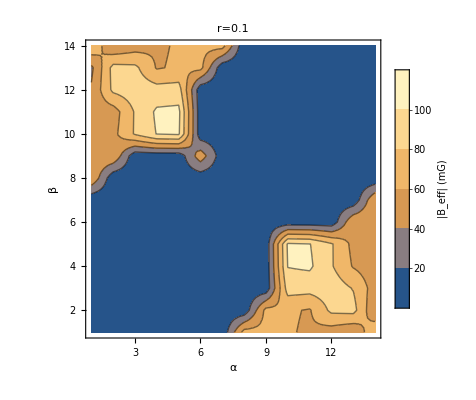
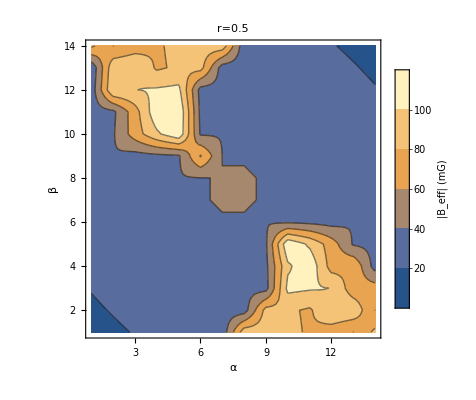
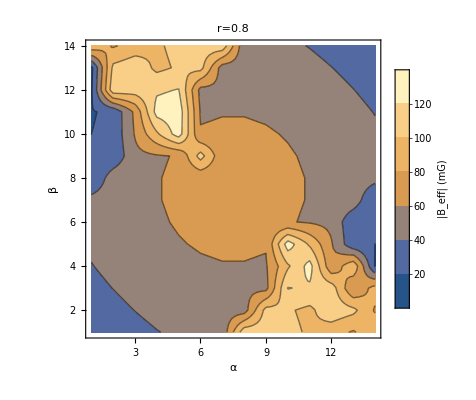
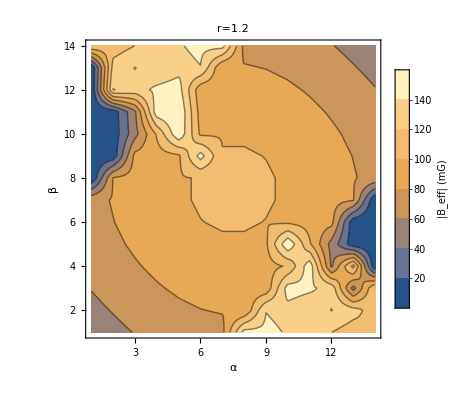
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{
r=0.1;
ListContourPlot[ Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1, PlotLabel -> "r=0.1"],

r=0.5;
ListContourPlot[ Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1,PlotLabel -> "r=0.5"]},
{

r=0.8;
ListContourPlot[ Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1, PlotLabel -> "r=0.8"],

r=1.2;
ListContourPlot[ Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1, PlotLabel -> "r=1.2"]


}}]
```

```mathematica
a= Pi/4; b = -Pi/4; r= 1
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}
Plot3D[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2},{b, -Pi/2, Pi/2},PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}]]
```

1

{0,{x→-3.4084×10^-7,y→-4.2605×10^-7,zf→-2.5563×10^-7}}

-Graphics3D-

```mathematica
Direction of Beff
```

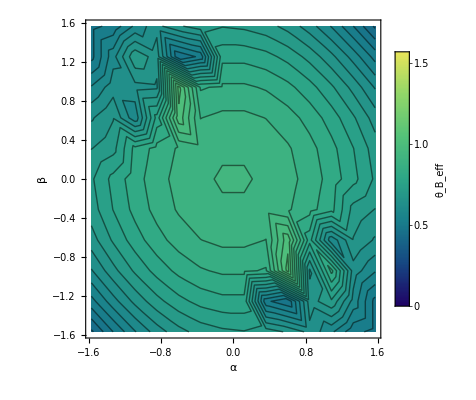

```mathematica
r=2.3;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, Pi/2}}], PlotRange->{ All, All, {0,Pi/2}}, Contours ->30, InterpolationOrder->5]
```

```mathematica
ToSphericalCoordinates[{0,-1,0}]
```

{1,π/2,-π/2}

```mathematica
ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]
```

1.34933

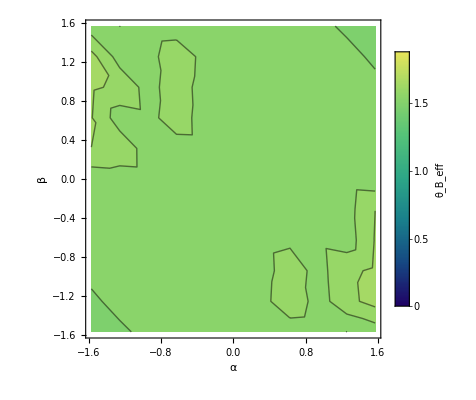
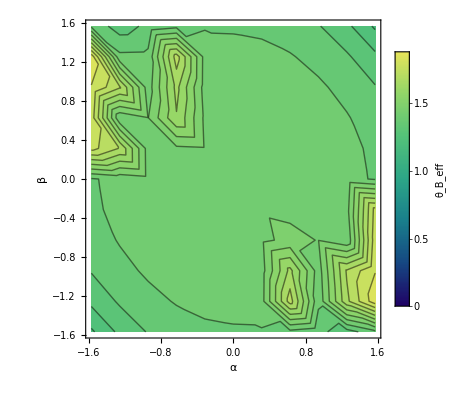
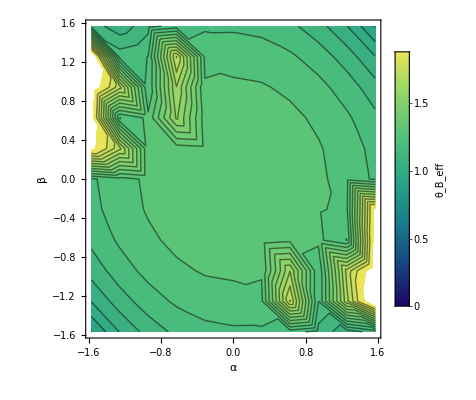
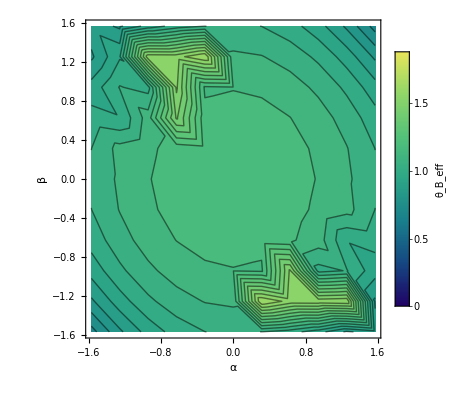
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{
r=0.1;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]
,

r=0.4;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]
},
{

r=0.8;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]
,

r=1.2;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]


}}]
```

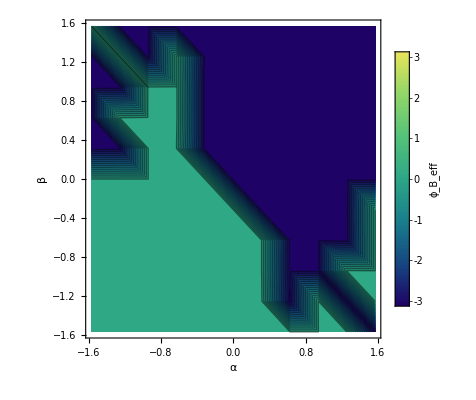
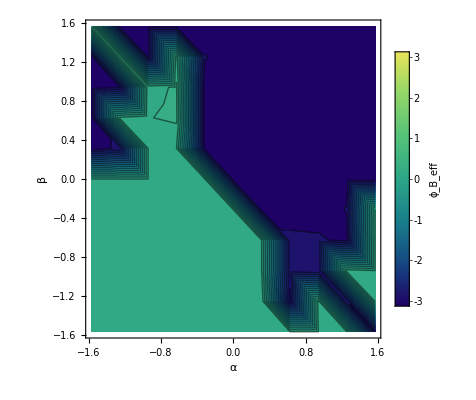
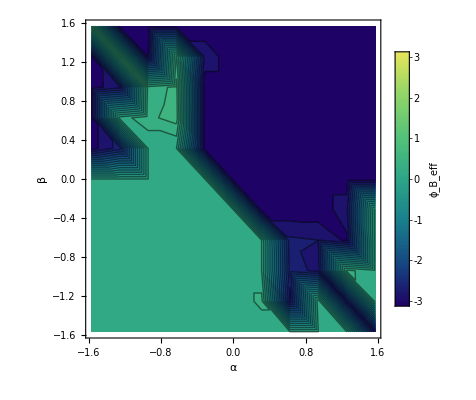
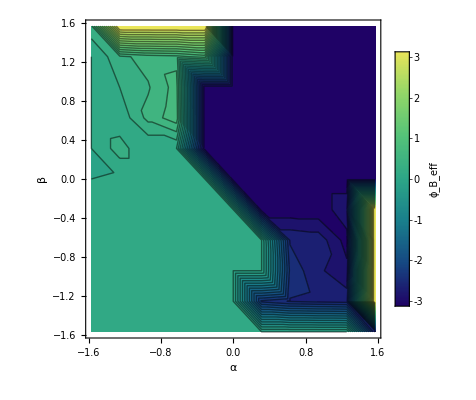
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{
r=0.1;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{-Pi,Pi}},None, LegendLabel-> "ϕ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{-Pi,Pi}}], PlotRange->{ All, All, {-Pi,Pi}}, Contours ->30, InterpolationOrder->5]
,

r=0.4;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{-Pi,Pi}},None, LegendLabel-> "ϕ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{-Pi,Pi}}], PlotRange->{ All, All, {-Pi,Pi}}, Contours ->30, InterpolationOrder->5]
},
{

r=0.8;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{-Pi,Pi}},None, LegendLabel-> "ϕ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{-Pi,Pi}}], PlotRange->{ All, All, {-Pi,Pi}}, Contours ->30, InterpolationOrder->5]
,

r=1.2;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{-Pi,Pi}},None, LegendLabel-> "ϕ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{-Pi,Pi}}], PlotRange->{ All, All, {-Pi,Pi}}, Contours ->30, InterpolationOrder->5]}}]
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

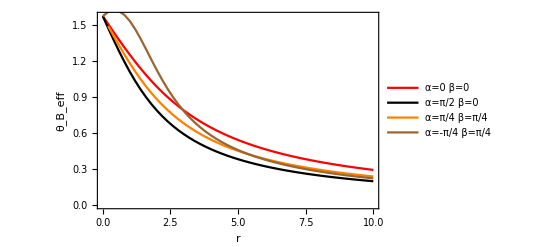

```mathematica
Show[{a= 0; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=0  β=0"}],Above]],
a= Pi/2; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Black, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=π/2  β=0"}],Above]],

a= Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Orange, FrameStyle-> Black, Frame-> True, PlotLegends->Placed[LineLegend[{"α=π/4  β=π/4"}],Above]],


a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Brown, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=-π/4  β=π/4"}],Above]]
}]
```

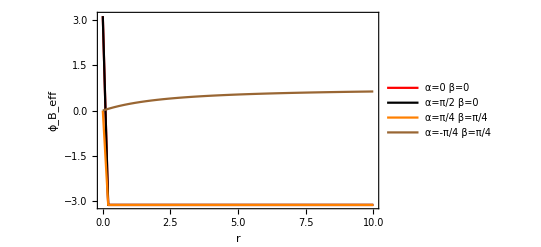

```mathematica
Show[{a= 0; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=0  β=0"}],Above]],
a= Pi/2; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Black, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=π/2  β=0"}],Above]],

a= Pi/3; b= Pi/3;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Orange, FrameStyle-> Black, Frame-> True, PlotLegends->Placed[LineLegend[{"α=π/4  β=π/4"}],Above]],


a= -Pi/3; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Brown, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=-π/4  β=π/4"}],Above]]
}]
```

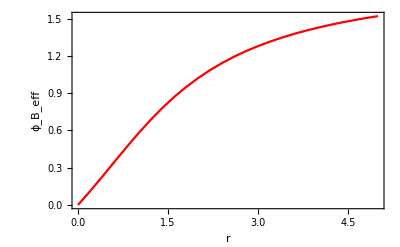

```mathematica
a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,5, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True]
```

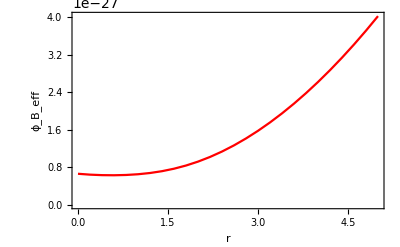

```mathematica
a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[1]]},{r, 0,5, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True]
```

## new lattice potential (doesnt make sense as lattice stays the same in spite of the new beam!!!!!)

```mathematica
udsimraw = +-2/3*hbar Gam^2 Inti / (Delta*8 Ints)ϵ1.ϵ1s//FullSimplify
```

```mathematica
UDsim[x_,y_,z_,a_,b_]:=-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])
```

{0,{x→-4.2605×10^-7,y→-4.2605×10^-7,zf→-4.2605×10^-7}}

-Graphics3D-

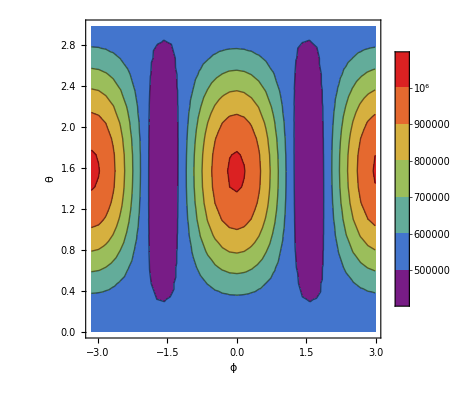

```mathematica
r=0;z=0;a= +Pi/4+Pi/18; +Pi/4+Pi/6;
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}
goodlat = Show[{ListPlot3D[Flatten[Table[{x,y,Sqrt[ecrosss[x,y,zf /. mi[[2]],a,b].ecrosss[x,y,zf /. mi[[2]],a,b]]*2*10^28-13},{x,-2λ,2λ, λ/10},{y,-2 λ,2λ,λ/10}],1], PlotStyle ->  {LightRed, Opacity[0.7]}],

ListPlot3D[Flatten[Table[{x,y,UDsim[x,y,zf /. mi[[2]],a,b]/Er},{x,-2λ,2λ, λ/10},{y,-2 λ,2λ,λ/10}],1]]

}, PlotRange -> All]


ho = 10^-9;
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
abola =Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

{ϕ,θ,(Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])])}

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}]; 
goodfreq = ListContourPlot[Flatten[abola,1], PlotLegends->True, ColorFunction-> "Rainbow", FrameLabel-> {"ϕ", "θ"}]
```

```mathematica
Flatten[Table[{x,y,ecrosss[x,y,zf /. mi[[2]],a,b].ecrosss[x,y,zf /. mi[[2]],a,b]},{x,-2λ,2λ, λ/10},{y,-2 λ,2λ,λ/10}],1]
```

{{-1.7042×10^-6,-1.7042×10^-6,5.17763×10^-55},{-1.7042×10^-6,-1.61899×10^-6,3.67475×10^-55},{-1.7042×10^-6,-1.53378×10^-6,2.45348×10^-55},1675,{1.7042×10^-6,1.53378×10^-6,5.36664×10^-55},{1.7042×10^-6,1.61899×10^-6,5.99758×10^-55},{1.7042×10^-6,1.7042×10^-6,5.17763×10^-55}}
 |  |  |  |

```mathematica
ListPlot3D[Flatten[Table[{x,y,UDsim[x,y,zf /. mi[[2]],a,b]/Er},{x,-2λ,2λ, λ/10},{y,-2 λ,2λ,λ/10}],1]]
```

-Graphics3D-